```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
data = Import["s_Distributions_Wishart5.csv"][[2;;,2;;17]];
```

```mathematica
mData = ArrayReshape[#,{4,4}]&/@data;
```

## ν = 5, 4x4 matrix, Ψ=Identity

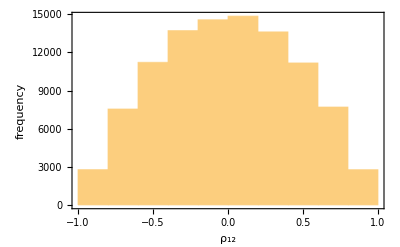

```mathematica
lRho12=mData[[All,1,2]]/(Sqrt[mData[[All,1,1]]]*Sqrt[mData[[All,2,2]]]);
g1=Histogram[lRho12,10,Frame->{True,True,False,False},FrameLabel->{"ρ_12","frequency"},BaseStyle->Medium]
```

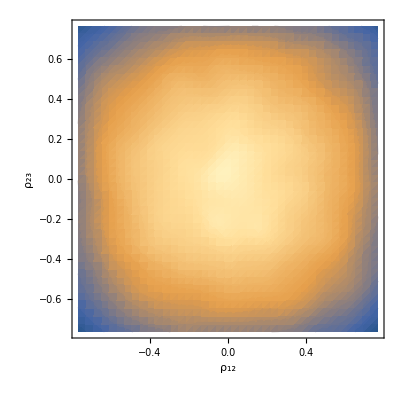

```mathematica
lRho23=mData[[All,2,3]]/(Sqrt[mData[[All,2,2]]]*Sqrt[mData[[All,3,3]]]);
g2=SmoothDensityHistogram[Thread[{lRho12,lRho23}],Mesh->10,Frame->{True,True,False,False},FrameLabel->{"ρ_12","ρ_23"},BaseStyle->Medium]
```

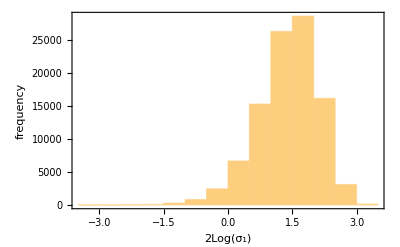

```mathematica
g3 = Histogram[Log@mData[[All,1,1]],Frame->{True,True,False,False},FrameLabel->{"2Log(σ_1)","frequency"},BaseStyle->Medium]
```

## ν = 5, 4x4 matrix, Ψ=Identity

```mathematica
data = Import["s_Distributions_Wishart50.csv"][[2;;,2;;17]];
```

```mathematica
mData = ArrayReshape[#,{4,4}]&/@data;
```

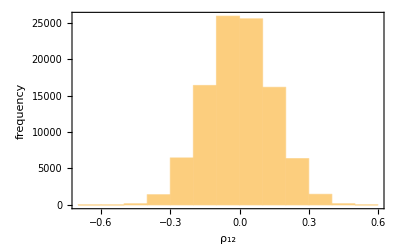

```mathematica
lRho12=mData[[All,1,2]]/(Sqrt[mData[[All,1,1]]]*Sqrt[mData[[All,2,2]]]);
g1=Histogram[lRho12,10,Frame->{True,True,False,False},FrameLabel->{"ρ_12","frequency"},BaseStyle->Medium]
```

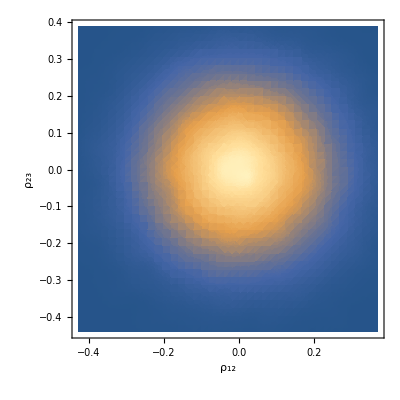

```mathematica
lRho23=mData[[All,2,3]]/(Sqrt[mData[[All,2,2]]]*Sqrt[mData[[All,3,3]]]);
g5=SmoothDensityHistogram[Thread[{lRho12,lRho23}],Mesh->10,Frame->{True,True,False,False},FrameLabel->{"ρ_12","ρ_23"},BaseStyle->Medium]
```

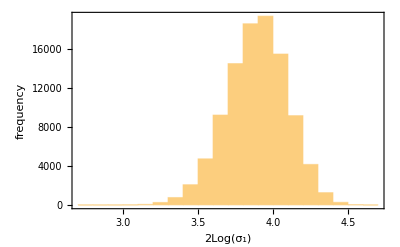

```mathematica
g6 = Histogram[Log@mData[[All,1,1]],Frame->{True,True,False,False},FrameLabel->{"2Log(σ_1)","frequency"},BaseStyle->Medium]
```